```mathematica
r = 0.15;
m = 22;
g = 9.81;
Subscript[I, w] = 0.005;
Subscript[I, s]=m*r^2;

Subscript[θ, 0d] = 30;
Subscript[θ, 0] = Subscript[θ, 0d] * Pi/180;
Subscript[ω, 0] = Pi;
k = 500;
```

```mathematica
DSolve[{x''[t] == -g/r*Sin[x[t]] - [t], x[0] == Subscript[θ, 0], x'[0] == 0}, x[t], t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[{x''[t]==-65.4 Sin[x[t]]-22.2222 x'[t],x[0]==0,x'[0]==0},x[t],t]

```mathematica
eq = -m*g*r*Sin[x[t]] - Subscript[I, w]*(x''[t]+k*x'[t]);
```

```mathematica
test =First[ x /.NDSolve[{Subscript[I, s]*x''[t] == eq, x[0] ==Subscript[θ, 0], x'[0] == Subscript[ω, 0]}, x,{t,0,3},AccuracyGoal->300]]
```

InterpolatingFunction[…]

```mathematica
motor = First[ x' /.NDSolve[{Subscript[I, s]*x''[t] == eq, x[0] == Subscript[θ, 0], x'[0] == Subscript[ω, 0]}, x',{t,0,3},AccuracyGoal->500]]
```

InterpolatingFunction[…]

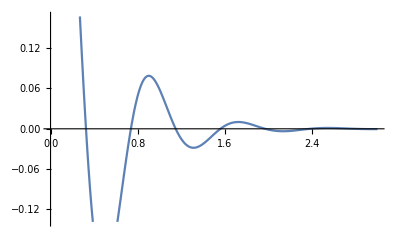

```mathematica
Plot[test[t], {t, 0, 3}]
```

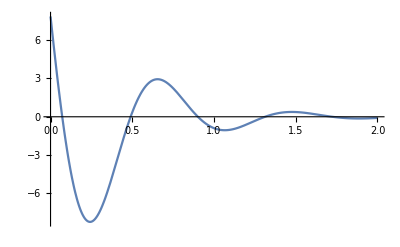

```mathematica
Plot[Subscript[I, w]*k*motor[t], {t, 0, 2}]
```

```mathematica
FindMaximum[Subscript[I, w]*k*motor[t], {t, 0, 3}]
```

InterpolatingFunction::dmval: Input value {-0.0579407} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0221314} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00845343} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{7.85398,{t→0.}}

```mathematica
NIntegrate[Subscript[I, w]*k*motor[t], {t, 0, 3}]
```

-0.327043

```mathematica
func=First[ x /.NDSolve[{x''[t] == -g/r*Sin[x[t]] - k/(m*r^2)*x'[t], x[0] == Subscript[θ, 0], x'[0] ==Subscript[ω, 0]}, x,{t,0,10}, AccuracyGoal->100, MaxStepFraction -> 1/100]]
```

InterpolatingFunction[…]

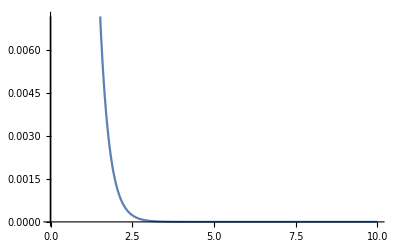

```mathematica
Plot[func[t], {t, 0, 10}]
```